# Calculation of LLP particle flux due to cosmic rays

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Set constants

```mathematica
c = 3*10^8;(*m/s*)
Gf =1.16638*10^(-5); (*GeV^-2*)
```

## Cosmic ray flux

Import cosmic ray flux data from Abe, Koh, et al. “Measurements of cosmic-ray proton and helium spectra from the BESS-Polar long-duration balloon flights over Antarctica.” The Astrophysical Journal 822.2 (2016): 65.

```mathematica
binList = Import["CRKeyVals.csv"];
binList =Delete[binList,1];
energyBins = Table[{binList[[i,2]],binList[[i,4]]},{i,1,Length[binList]}];
energyWidth = Table[binList[[i+69,5]],{i,1,20}];
```

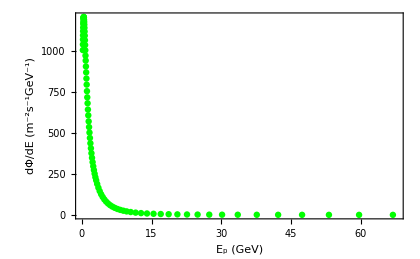

```mathematica
ListPlot[energyBins,FrameLabel->{"E_p (GeV)","dΦ/dE (m^-2s^-1GeV^-1)"},Frame->True,LabelStyle->{Black,15},ImageSize->420,PlotStyle->Directive[Green,Thick]]
```

```mathematica
energyBins
```

{{0.206,1004.75},{0.218,1039},{0.231,1069.15},{0.244,1094.75},{0.259,1120},{0.274,1142},{0.29,1164.15},{0.307,1176.45},{0.326,1193.45},{0.345,1200.85},{0.366,1204.5},{0.387,1207.05},{0.41,1206.05},{0.435,1202.45},{0.46,1188.8},{0.487,1176.15},{0.516,1160.3},{0.547,1140.55},{0.579,1118.05},{0.614,1092.75},{0.65,1064.95},{0.688,1035.8},{0.729,1003.7},{0.772,971.1},{0.818,940.8},{0.866,905.05},{0.918,868.9},{0.972,831.4},{1.03,794.3},{1.091,754.35},{1.156,716.65},{1.224,680.6},{1.297,642.2},{1.374,606.95},{1.455,570.05},{1.541,535.55},{1.632,501.95},{1.729,468.9},{1.831,436.6},{1.94,406},{2.054,376.05},{2.176,347.95},{2.305,321.6},{2.442,296.25},{2.587,273.25},{2.74,250.95},{2.902,229.5},{3.074,210.55},{3.289,188.5},{3.551,165.7},{3.834,144.8},{4.14,126},{4.471,109.3},{4.827,94.38},{5.212,81.165},{5.628,69.605},{6.077,59.325},{6.562,50.475},{7.085,42.82},{7.65,36.1},{8.26,30.495},{8.919,25.505},{9.631,21.305},{10.505,17.395},{11.565,13.775},{12.73,10.91},{14.01,8.5975},{15.42,6.7365},{16.97,5.2745},{18.675,4.13},{20.555,3.209},{22.625,2.497},{24.905,1.9275},{27.415,1.4995},{30.175,1.157},{33.55,0.87225},{37.645,0.6363},{42.24,0.4644},{47.395,0.3392},{53.175,0.2481},{59.665,0.1807},{66.945,0.1315},{75.11,0.09677},{84.28,0.07018},{94.565,0.05062},{106.8,0.037575},{121.4,0.02622},{138,0.01871},{156.8,0.013255}}

```mathematica
intEB=Interpolation[energyBins,InterpolationOrder->1]
```

InterpolatingFunction[…]

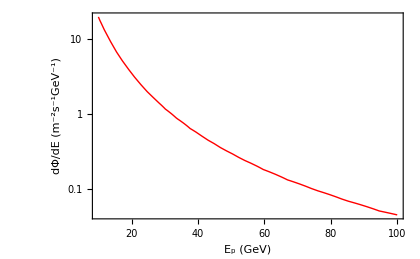

```mathematica
LogPlot[intEB[Ep],{Ep,10,100},FrameLabel->{"E_p (GeV)","dΦ/dE (m^-2s^-1GeV^-1)"},Frame->True,LabelStyle->{Black,15},ImageSize->420,PlotStyle->Directive[Red,Thick]]
```

## Pythia hadronization

First, we import the kaon results from our 10,000 event pythia runs.

```mathematica
For[i = 1, i <21, i++,  
If[i <10,
kaonPData[i]=Import[FileNameJoin[{NotebookDirectory[],"Data","ProtonScatter","kaonPData0" <>ToString[i]<>".txt"}],"table"];
kaonNData[i]=Import[FileNameJoin[{NotebookDirectory[],"Data","NeutronScatter","kaonNData0" <>ToString[i]<>".txt"}],"table"],kaonPData[i]=Import[FileNameJoin[{NotebookDirectory[],"Data","ProtonScatter","kaonPData" <>ToString[i]<>".txt"}],"table"];kaonNData[i]=Import[FileNameJoin[{NotebookDirectory[],"Data","NeutronScatter","kaonNData" <>ToString[i]<>".txt"}],"table"]
]

]
```

Test nested list element selection

```mathematica
kaonNData[1][[1]]
kaonNData[1][[1,3]]
kaonNData[1][[2]]
```

{Beams:eA,=,18.675}

18.675

{0,3.9598}

Calculate number of kaons produced for a given energy bin

```mathematica
For[i = 1, i <21, i++,  
numPKaons[i]=Times@@Dimensions[kaonPData[i]]-1;
numNKaons[i]=Times@@Dimensions[kaonNData[i]]-1;
numKaons[i] = numNKaons[i]+numPKaons[i]
]
```

```mathematica
numPKaons[1];
numNKaons[1];
numKaons[1];
```

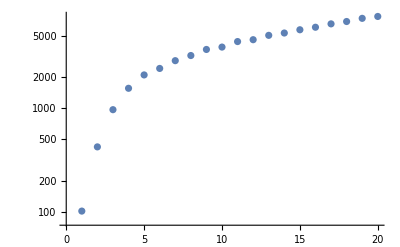

```mathematica
ListLogPlot[Table[numPKaons[i],{i,1,20}]]
```

Obtain a probability distribution of kaons over energy

### Tests

```mathematica
testkEngPoints=Table[kaonData[1][[j,2]],{j,2,numKaons[1]+1}]
```

Part::partw: Part 2 of kaonData[1] does not exist.

Part::partw: Part 3 of kaonData[1] does not exist.

Part::partw: Part 4 of kaonData[1] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{kaonData[1]⟦2,2⟧,kaonData[1]⟦3,2⟧,kaonData[1]⟦4,2⟧,kaonData[1]⟦5,2⟧,kaonData[1]⟦6,2⟧,kaonData[1]⟦7,2⟧,kaonData[1]⟦8,2⟧,kaonData[1]⟦9,2⟧,kaonData[1]⟦10,2⟧,kaonData[1]⟦11,2⟧,kaonData[1]⟦12,2⟧,kaonData[1]⟦13,2⟧,kaonData[1]⟦14,2⟧,kaonData[1]⟦15,2⟧,kaonData[1]⟦16,2⟧,kaonData[1]⟦17,2⟧,kaonData[1]⟦18,2⟧,kaonData[1]⟦19,2⟧,kaonData[1]⟦20,2⟧,kaonData[1]⟦21,2⟧,kaonData[1]⟦22,2⟧,kaonData[1]⟦23,2⟧,kaonData[1]⟦24,2⟧,kaonData[1]⟦25,2⟧,kaonData[1]⟦26,2⟧,kaonData[1]⟦27,2⟧,kaonData[1]⟦28,2⟧,kaonData[1]⟦29,2⟧,kaonData[1]⟦30,2⟧,kaonData[1]⟦31,2⟧,kaonData[1]⟦32,2⟧,kaonData[1]⟦33,2⟧,kaonData[1]⟦34,2⟧,kaonData[1]⟦35,2⟧,kaonData[1]⟦36,2⟧,kaonData[1]⟦37,2⟧,kaonData[1]⟦38,2⟧,kaonData[1]⟦39,2⟧,kaonData[1]⟦40,2⟧,kaonData[1]⟦41,2⟧,kaonData[1]⟦42,2⟧,kaonData[1]⟦43,2⟧,kaonData[1]⟦44,2⟧,kaonData[1]⟦45,2⟧,kaonData[1]⟦46,2⟧,kaonData[1]⟦47,2⟧,kaonData[1]⟦48,2⟧,kaonData[1]⟦49,2⟧,kaonData[1]⟦50,2⟧,kaonData[1]⟦51,2⟧,kaonData[1]⟦52,2⟧,kaonData[1]⟦53,2⟧,kaonData[1]⟦54,2⟧,kaonData[1]⟦55,2⟧,kaonData[1]⟦56,2⟧,kaonData[1]⟦57,2⟧,kaonData[1]⟦58,2⟧,kaonData[1]⟦59,2⟧,kaonData[1]⟦60,2⟧,kaonData[1]⟦61,2⟧,kaonData[1]⟦62,2⟧,kaonData[1]⟦63,2⟧,kaonData[1]⟦64,2⟧,kaonData[1]⟦65,2⟧,kaonData[1]⟦66,2⟧,kaonData[1]⟦67,2⟧,kaonData[1]⟦68,2⟧,kaonData[1]⟦69,2⟧,kaonData[1]⟦70,2⟧,kaonData[1]⟦71,2⟧,kaonData[1]⟦72,2⟧,kaonData[1]⟦73,2⟧,kaonData[1]⟦74,2⟧,kaonData[1]⟦75,2⟧,kaonData[1]⟦76,2⟧,kaonData[1]⟦77,2⟧,kaonData[1]⟦78,2⟧,kaonData[1]⟦79,2⟧,kaonData[1]⟦80,2⟧,kaonData[1]⟦81,2⟧,kaonData[1]⟦82,2⟧,kaonData[1]⟦83,2⟧,kaonData[1]⟦84,2⟧,kaonData[1]⟦85,2⟧,kaonData[1]⟦86,2⟧,kaonData[1]⟦87,2⟧,kaonData[1]⟦88,2⟧,kaonData[1]⟦89,2⟧,kaonData[1]⟦90,2⟧,kaonData[1]⟦91,2⟧,kaonData[1]⟦92,2⟧,kaonData[1]⟦93,2⟧,kaonData[1]⟦94,2⟧,kaonData[1]⟦95,2⟧,kaonData[1]⟦96,2⟧,kaonData[1]⟦97,2⟧,kaonData[1]⟦98,2⟧,kaonData[1]⟦99,2⟧,kaonData[1]⟦100,2⟧,kaonData[1]⟦101,2⟧,kaonData[1]⟦102,2⟧,kaonData[1]⟦103,2⟧,kaonData[1]⟦104,2⟧,kaonData[1]⟦105,2⟧,kaonData[1]⟦106,2⟧,kaonData[1]⟦107,2⟧,kaonData[1]⟦108,2⟧,kaonData[1]⟦109,2⟧,kaonData[1]⟦110,2⟧,kaonData[1]⟦111,2⟧,kaonData[1]⟦112,2⟧,kaonData[1]⟦113,2⟧,kaonData[1]⟦114,2⟧,kaonData[1]⟦115,2⟧,kaonData[1]⟦116,2⟧,kaonData[1]⟦117,2⟧,kaonData[1]⟦118,2⟧,kaonData[1]⟦119,2⟧,kaonData[1]⟦120,2⟧,kaonData[1]⟦121,2⟧,kaonData[1]⟦122,2⟧,kaonData[1]⟦123,2⟧,kaonData[1]⟦124,2⟧,kaonData[1]⟦125,2⟧,kaonData[1]⟦126,2⟧,kaonData[1]⟦127,2⟧,kaonData[1]⟦128,2⟧,kaonData[1]⟦129,2⟧,kaonData[1]⟦130,2⟧,kaonData[1]⟦131,2⟧,kaonData[1]⟦132,2⟧,kaonData[1]⟦133,2⟧,kaonData[1]⟦134,2⟧,kaonData[1]⟦135,2⟧,kaonData[1]⟦136,2⟧,kaonData[1]⟦137,2⟧,kaonData[1]⟦138,2⟧,kaonData[1]⟦139,2⟧,kaonData[1]⟦140,2⟧,kaonData[1]⟦141,2⟧,kaonData[1]⟦142,2⟧,kaonData[1]⟦143,2⟧,kaonData[1]⟦144,2⟧,kaonData[1]⟦145,2⟧,kaonData[1]⟦146,2⟧,kaonData[1]⟦147,2⟧,kaonData[1]⟦148,2⟧,kaonData[1]⟦149,2⟧,kaonData[1]⟦150,2⟧,kaonData[1]⟦151,2⟧,kaonData[1]⟦152,2⟧,kaonData[1]⟦153,2⟧,kaonData[1]⟦154,2⟧,kaonData[1]⟦155,2⟧,kaonData[1]⟦156,2⟧,kaonData[1]⟦157,2⟧,kaonData[1]⟦158,2⟧,kaonData[1]⟦159,2⟧,kaonData[1]⟦160,2⟧,kaonData[1]⟦161,2⟧,kaonData[1]⟦162,2⟧,kaonData[1]⟦163,2⟧,kaonData[1]⟦164,2⟧,kaonData[1]⟦165,2⟧,kaonData[1]⟦166,2⟧,kaonData[1]⟦167,2⟧,kaonData[1]⟦168,2⟧,kaonData[1]⟦169,2⟧,kaonData[1]⟦170,2⟧,kaonData[1]⟦171,2⟧,kaonData[1]⟦172,2⟧,kaonData[1]⟦173,2⟧,kaonData[1]⟦174,2⟧,kaonData[1]⟦175,2⟧,kaonData[1]⟦176,2⟧,kaonData[1]⟦177,2⟧,kaonData[1]⟦178,2⟧,kaonData[1]⟦179,2⟧,kaonData[1]⟦180,2⟧,kaonData[1]⟦181,2⟧,kaonData[1]⟦182,2⟧,kaonData[1]⟦183,2⟧,kaonData[1]⟦184,2⟧,kaonData[1]⟦185,2⟧,kaonData[1]⟦186,2⟧,kaonData[1]⟦187,2⟧,kaonData[1]⟦188,2⟧,kaonData[1]⟦189,2⟧,kaonData[1]⟦190,2⟧,kaonData[1]⟦191,2⟧,kaonData[1]⟦192,2⟧,kaonData[1]⟦193,2⟧,kaonData[1]⟦194,2⟧,kaonData[1]⟦195,2⟧,kaonData[1]⟦196,2⟧,kaonData[1]⟦197,2⟧,kaonData[1]⟦198,2⟧,kaonData[1]⟦199,2⟧,kaonData[1]⟦200,2⟧,kaonData[1]⟦201,2⟧,kaonData[1]⟦202,2⟧,kaonData[1]⟦203,2⟧,kaonData[1]⟦204,2⟧,kaonData[1]⟦205,2⟧,kaonData[1]⟦206,2⟧,kaonData[1]⟦207,2⟧,kaonData[1]⟦208,2⟧,kaonData[1]⟦209,2⟧,kaonData[1]⟦210,2⟧,kaonData[1]⟦211,2⟧,kaonData[1]⟦212,2⟧,kaonData[1]⟦213,2⟧}

```mathematica
testsmoothkEng =SmoothKernelDistribution[testkEngPoints]
testsmoothkEng2 =SmoothKernelDistribution[Flatten@testkEngPoints,0.5]
```

SmoothKernelDistribution::invldd: The input data SmoothKernelDistribution[{kaonData[1]⟦2,2⟧,kaonData[1]⟦3,2⟧,kaonData[1]⟦4,2⟧,kaonData[1]⟦5,2⟧,kaonData[1]⟦6,2⟧,kaonData[1]⟦7,2⟧,kaonData[1]⟦8,2⟧,kaonData[1]⟦9,2⟧,kaonData[1]⟦10,2⟧,kaonData[1]⟦11,2⟧,kaonData[1]⟦12,2⟧,kaonData[1]⟦13,2⟧,kaonData[1]⟦14,2⟧,kaonData[1]⟦15,2⟧,«23»,kaonData[1]⟦39,2⟧,kaonData[1]⟦40,2⟧,kaonData[1]⟦41,2⟧,kaonData[1]⟦42,2⟧,kaonData[1]⟦43,2⟧,kaonData[1]⟦44,2⟧,kaonData[1]⟦45,2⟧,kaonData[1]⟦46,2⟧,kaonData[1]⟦47,2⟧,kaonData[1]⟦48,2⟧,kaonData[1]⟦49,2⟧,kaonData[1]⟦50,2⟧,kaonData[1]⟦51,2⟧,«162»}] should be a vector or a matrix of real numbers or a valid TemporalData object.

SmoothKernelDistribution[{kaonData[1]⟦2,2⟧,kaonData[1]⟦3,2⟧,kaonData[1]⟦4,2⟧,kaonData[1]⟦5,2⟧,kaonData[1]⟦6,2⟧,kaonData[1]⟦7,2⟧,kaonData[1]⟦8,2⟧,kaonData[1]⟦9,2⟧,kaonData[1]⟦10,2⟧,kaonData[1]⟦11,2⟧,kaonData[1]⟦12,2⟧,kaonData[1]⟦13,2⟧,kaonData[1]⟦14,2⟧,kaonData[1]⟦15,2⟧,kaonData[1]⟦16,2⟧,kaonData[1]⟦17,2⟧,kaonData[1]⟦18,2⟧,kaonData[1]⟦19,2⟧,kaonData[1]⟦20,2⟧,kaonData[1]⟦21,2⟧,kaonData[1]⟦22,2⟧,kaonData[1]⟦23,2⟧,kaonData[1]⟦24,2⟧,kaonData[1]⟦25,2⟧,kaonData[1]⟦26,2⟧,kaonData[1]⟦27,2⟧,kaonData[1]⟦28,2⟧,kaonData[1]⟦29,2⟧,kaonData[1]⟦30,2⟧,kaonData[1]⟦31,2⟧,kaonData[1]⟦32,2⟧,kaonData[1]⟦33,2⟧,kaonData[1]⟦34,2⟧,kaonData[1]⟦35,2⟧,kaonData[1]⟦36,2⟧,kaonData[1]⟦37,2⟧,kaonData[1]⟦38,2⟧,kaonData[1]⟦39,2⟧,kaonData[1]⟦40,2⟧,kaonData[1]⟦41,2⟧,kaonData[1]⟦42,2⟧,kaonData[1]⟦43,2⟧,kaonData[1]⟦44,2⟧,kaonData[1]⟦45,2⟧,kaonData[1]⟦46,2⟧,kaonData[1]⟦47,2⟧,kaonData[1]⟦48,2⟧,kaonData[1]⟦49,2⟧,kaonData[1]⟦50,2⟧,kaonData[1]⟦51,2⟧,kaonData[1]⟦52,2⟧,kaonData[1]⟦53,2⟧,kaonData[1]⟦54,2⟧,kaonData[1]⟦55,2⟧,kaonData[1]⟦56,2⟧,kaonData[1]⟦57,2⟧,kaonData[1]⟦58,2⟧,kaonData[1]⟦59,2⟧,kaonData[1]⟦60,2⟧,kaonData[1]⟦61,2⟧,kaonData[1]⟦62,2⟧,kaonData[1]⟦63,2⟧,kaonData[1]⟦64,2⟧,kaonData[1]⟦65,2⟧,kaonData[1]⟦66,2⟧,kaonData[1]⟦67,2⟧,kaonData[1]⟦68,2⟧,kaonData[1]⟦69,2⟧,kaonData[1]⟦70,2⟧,kaonData[1]⟦71,2⟧,kaonData[1]⟦72,2⟧,kaonData[1]⟦73,2⟧,kaonData[1]⟦74,2⟧,kaonData[1]⟦75,2⟧,kaonData[1]⟦76,2⟧,kaonData[1]⟦77,2⟧,kaonData[1]⟦78,2⟧,kaonData[1]⟦79,2⟧,kaonData[1]⟦80,2⟧,kaonData[1]⟦81,2⟧,kaonData[1]⟦82,2⟧,kaonData[1]⟦83,2⟧,kaonData[1]⟦84,2⟧,kaonData[1]⟦85,2⟧,kaonData[1]⟦86,2⟧,kaonData[1]⟦87,2⟧,kaonData[1]⟦88,2⟧,kaonData[1]⟦89,2⟧,kaonData[1]⟦90,2⟧,kaonData[1]⟦91,2⟧,kaonData[1]⟦92,2⟧,kaonData[1]⟦93,2⟧,kaonData[1]⟦94,2⟧,kaonData[1]⟦95,2⟧,kaonData[1]⟦96,2⟧,kaonData[1]⟦97,2⟧,kaonData[1]⟦98,2⟧,kaonData[1]⟦99,2⟧,kaonData[1]⟦100,2⟧,kaonData[1]⟦101,2⟧,kaonData[1]⟦102,2⟧,kaonData[1]⟦103,2⟧,kaonData[1]⟦104,2⟧,kaonData[1]⟦105,2⟧,kaonData[1]⟦106,2⟧,kaonData[1]⟦107,2⟧,kaonData[1]⟦108,2⟧,kaonData[1]⟦109,2⟧,kaonData[1]⟦110,2⟧,kaonData[1]⟦111,2⟧,kaonData[1]⟦112,2⟧,kaonData[1]⟦113,2⟧,kaonData[1]⟦114,2⟧,kaonData[1]⟦115,2⟧,kaonData[1]⟦116,2⟧,kaonData[1]⟦117,2⟧,kaonData[1]⟦118,2⟧,kaonData[1]⟦119,2⟧,kaonData[1]⟦120,2⟧,kaonData[1]⟦121,2⟧,kaonData[1]⟦122,2⟧,kaonData[1]⟦123,2⟧,kaonData[1]⟦124,2⟧,kaonData[1]⟦125,2⟧,kaonData[1]⟦126,2⟧,kaonData[1]⟦127,2⟧,kaonData[1]⟦128,2⟧,kaonData[1]⟦129,2⟧,kaonData[1]⟦130,2⟧,kaonData[1]⟦131,2⟧,kaonData[1]⟦132,2⟧,kaonData[1]⟦133,2⟧,kaonData[1]⟦134,2⟧,kaonData[1]⟦135,2⟧,kaonData[1]⟦136,2⟧,kaonData[1]⟦137,2⟧,kaonData[1]⟦138,2⟧,kaonData[1]⟦139,2⟧,kaonData[1]⟦140,2⟧,kaonData[1]⟦141,2⟧,kaonData[1]⟦142,2⟧,kaonData[1]⟦143,2⟧,kaonData[1]⟦144,2⟧,kaonData[1]⟦145,2⟧,kaonData[1]⟦146,2⟧,kaonData[1]⟦147,2⟧,kaonData[1]⟦148,2⟧,kaonData[1]⟦149,2⟧,kaonData[1]⟦150,2⟧,kaonData[1]⟦151,2⟧,kaonData[1]⟦152,2⟧,kaonData[1]⟦153,2⟧,kaonData[1]⟦154,2⟧,kaonData[1]⟦155,2⟧,kaonData[1]⟦156,2⟧,kaonData[1]⟦157,2⟧,kaonData[1]⟦158,2⟧,kaonData[1]⟦159,2⟧,kaonData[1]⟦160,2⟧,kaonData[1]⟦161,2⟧,kaonData[1]⟦162,2⟧,kaonData[1]⟦163,2⟧,kaonData[1]⟦164,2⟧,kaonData[1]⟦165,2⟧,kaonData[1]⟦166,2⟧,kaonData[1]⟦167,2⟧,kaonData[1]⟦168,2⟧,kaonData[1]⟦169,2⟧,kaonData[1]⟦170,2⟧,kaonData[1]⟦171,2⟧,kaonData[1]⟦172,2⟧,kaonData[1]⟦173,2⟧,kaonData[1]⟦174,2⟧,kaonData[1]⟦175,2⟧,kaonData[1]⟦176,2⟧,kaonData[1]⟦177,2⟧,kaonData[1]⟦178,2⟧,kaonData[1]⟦179,2⟧,kaonData[1]⟦180,2⟧,kaonData[1]⟦181,2⟧,kaonData[1]⟦182,2⟧,kaonData[1]⟦183,2⟧,kaonData[1]⟦184,2⟧,kaonData[1]⟦185,2⟧,kaonData[1]⟦186,2⟧,kaonData[1]⟦187,2⟧,kaonData[1]⟦188,2⟧,kaonData[1]⟦189,2⟧,kaonData[1]⟦190,2⟧,kaonData[1]⟦191,2⟧,kaonData[1]⟦192,2⟧,kaonData[1]⟦193,2⟧,kaonData[1]⟦194,2⟧,kaonData[1]⟦195,2⟧,kaonData[1]⟦196,2⟧,kaonData[1]⟦197,2⟧,kaonData[1]⟦198,2⟧,kaonData[1]⟦199,2⟧,kaonData[1]⟦200,2⟧,kaonData[1]⟦201,2⟧,kaonData[1]⟦202,2⟧,kaonData[1]⟦203,2⟧,kaonData[1]⟦204,2⟧,kaonData[1]⟦205,2⟧,kaonData[1]⟦206,2⟧,kaonData[1]⟦207,2⟧,kaonData[1]⟦208,2⟧,kaonData[1]⟦209,2⟧,kaonData[1]⟦210,2⟧,kaonData[1]⟦211,2⟧,kaonData[1]⟦212,2⟧,kaonData[1]⟦213,2⟧}]

SmoothKernelDistribution::invldd: The input data SmoothKernelDistribution[{kaonData[1]⟦2,2⟧,kaonData[1]⟦3,2⟧,kaonData[1]⟦4,2⟧,kaonData[1]⟦5,2⟧,kaonData[1]⟦6,2⟧,kaonData[1]⟦7,2⟧,kaonData[1]⟦8,2⟧,kaonData[1]⟦9,2⟧,kaonData[1]⟦10,2⟧,kaonData[1]⟦11,2⟧,kaonData[1]⟦12,2⟧,kaonData[1]⟦13,2⟧,kaonData[1]⟦14,2⟧,kaonData[1]⟦15,2⟧,«23»,kaonData[1]⟦39,2⟧,kaonData[1]⟦40,2⟧,kaonData[1]⟦41,2⟧,kaonData[1]⟦42,2⟧,kaonData[1]⟦43,2⟧,kaonData[1]⟦44,2⟧,kaonData[1]⟦45,2⟧,kaonData[1]⟦46,2⟧,kaonData[1]⟦47,2⟧,kaonData[1]⟦48,2⟧,kaonData[1]⟦49,2⟧,kaonData[1]⟦50,2⟧,kaonData[1]⟦51,2⟧,«162»}] should be a vector or a matrix of real numbers or a valid TemporalData object.

SmoothKernelDistribution[{kaonData[1]⟦2,2⟧,kaonData[1]⟦3,2⟧,kaonData[1]⟦4,2⟧,kaonData[1]⟦5,2⟧,kaonData[1]⟦6,2⟧,kaonData[1]⟦7,2⟧,kaonData[1]⟦8,2⟧,kaonData[1]⟦9,2⟧,kaonData[1]⟦10,2⟧,kaonData[1]⟦11,2⟧,kaonData[1]⟦12,2⟧,kaonData[1]⟦13,2⟧,kaonData[1]⟦14,2⟧,kaonData[1]⟦15,2⟧,kaonData[1]⟦16,2⟧,kaonData[1]⟦17,2⟧,kaonData[1]⟦18,2⟧,kaonData[1]⟦19,2⟧,kaonData[1]⟦20,2⟧,kaonData[1]⟦21,2⟧,kaonData[1]⟦22,2⟧,kaonData[1]⟦23,2⟧,kaonData[1]⟦24,2⟧,kaonData[1]⟦25,2⟧,kaonData[1]⟦26,2⟧,kaonData[1]⟦27,2⟧,kaonData[1]⟦28,2⟧,kaonData[1]⟦29,2⟧,kaonData[1]⟦30,2⟧,kaonData[1]⟦31,2⟧,kaonData[1]⟦32,2⟧,kaonData[1]⟦33,2⟧,kaonData[1]⟦34,2⟧,kaonData[1]⟦35,2⟧,kaonData[1]⟦36,2⟧,kaonData[1]⟦37,2⟧,kaonData[1]⟦38,2⟧,kaonData[1]⟦39,2⟧,kaonData[1]⟦40,2⟧,kaonData[1]⟦41,2⟧,kaonData[1]⟦42,2⟧,kaonData[1]⟦43,2⟧,kaonData[1]⟦44,2⟧,kaonData[1]⟦45,2⟧,kaonData[1]⟦46,2⟧,kaonData[1]⟦47,2⟧,kaonData[1]⟦48,2⟧,kaonData[1]⟦49,2⟧,kaonData[1]⟦50,2⟧,kaonData[1]⟦51,2⟧,kaonData[1]⟦52,2⟧,kaonData[1]⟦53,2⟧,kaonData[1]⟦54,2⟧,kaonData[1]⟦55,2⟧,kaonData[1]⟦56,2⟧,kaonData[1]⟦57,2⟧,kaonData[1]⟦58,2⟧,kaonData[1]⟦59,2⟧,kaonData[1]⟦60,2⟧,kaonData[1]⟦61,2⟧,kaonData[1]⟦62,2⟧,kaonData[1]⟦63,2⟧,kaonData[1]⟦64,2⟧,kaonData[1]⟦65,2⟧,kaonData[1]⟦66,2⟧,kaonData[1]⟦67,2⟧,kaonData[1]⟦68,2⟧,kaonData[1]⟦69,2⟧,kaonData[1]⟦70,2⟧,kaonData[1]⟦71,2⟧,kaonData[1]⟦72,2⟧,kaonData[1]⟦73,2⟧,kaonData[1]⟦74,2⟧,kaonData[1]⟦75,2⟧,kaonData[1]⟦76,2⟧,kaonData[1]⟦77,2⟧,kaonData[1]⟦78,2⟧,kaonData[1]⟦79,2⟧,kaonData[1]⟦80,2⟧,kaonData[1]⟦81,2⟧,kaonData[1]⟦82,2⟧,kaonData[1]⟦83,2⟧,kaonData[1]⟦84,2⟧,kaonData[1]⟦85,2⟧,kaonData[1]⟦86,2⟧,kaonData[1]⟦87,2⟧,kaonData[1]⟦88,2⟧,kaonData[1]⟦89,2⟧,kaonData[1]⟦90,2⟧,kaonData[1]⟦91,2⟧,kaonData[1]⟦92,2⟧,kaonData[1]⟦93,2⟧,kaonData[1]⟦94,2⟧,kaonData[1]⟦95,2⟧,kaonData[1]⟦96,2⟧,kaonData[1]⟦97,2⟧,kaonData[1]⟦98,2⟧,kaonData[1]⟦99,2⟧,kaonData[1]⟦100,2⟧,kaonData[1]⟦101,2⟧,kaonData[1]⟦102,2⟧,kaonData[1]⟦103,2⟧,kaonData[1]⟦104,2⟧,kaonData[1]⟦105,2⟧,kaonData[1]⟦106,2⟧,kaonData[1]⟦107,2⟧,kaonData[1]⟦108,2⟧,kaonData[1]⟦109,2⟧,kaonData[1]⟦110,2⟧,kaonData[1]⟦111,2⟧,kaonData[1]⟦112,2⟧,kaonData[1]⟦113,2⟧,kaonData[1]⟦114,2⟧,kaonData[1]⟦115,2⟧,kaonData[1]⟦116,2⟧,kaonData[1]⟦117,2⟧,kaonData[1]⟦118,2⟧,kaonData[1]⟦119,2⟧,kaonData[1]⟦120,2⟧,kaonData[1]⟦121,2⟧,kaonData[1]⟦122,2⟧,kaonData[1]⟦123,2⟧,kaonData[1]⟦124,2⟧,kaonData[1]⟦125,2⟧,kaonData[1]⟦126,2⟧,kaonData[1]⟦127,2⟧,kaonData[1]⟦128,2⟧,kaonData[1]⟦129,2⟧,kaonData[1]⟦130,2⟧,kaonData[1]⟦131,2⟧,kaonData[1]⟦132,2⟧,kaonData[1]⟦133,2⟧,kaonData[1]⟦134,2⟧,kaonData[1]⟦135,2⟧,kaonData[1]⟦136,2⟧,kaonData[1]⟦137,2⟧,kaonData[1]⟦138,2⟧,kaonData[1]⟦139,2⟧,kaonData[1]⟦140,2⟧,kaonData[1]⟦141,2⟧,kaonData[1]⟦142,2⟧,kaonData[1]⟦143,2⟧,kaonData[1]⟦144,2⟧,kaonData[1]⟦145,2⟧,kaonData[1]⟦146,2⟧,kaonData[1]⟦147,2⟧,kaonData[1]⟦148,2⟧,kaonData[1]⟦149,2⟧,kaonData[1]⟦150,2⟧,kaonData[1]⟦151,2⟧,kaonData[1]⟦152,2⟧,kaonData[1]⟦153,2⟧,kaonData[1]⟦154,2⟧,kaonData[1]⟦155,2⟧,kaonData[1]⟦156,2⟧,kaonData[1]⟦157,2⟧,kaonData[1]⟦158,2⟧,kaonData[1]⟦159,2⟧,kaonData[1]⟦160,2⟧,kaonData[1]⟦161,2⟧,kaonData[1]⟦162,2⟧,kaonData[1]⟦163,2⟧,kaonData[1]⟦164,2⟧,kaonData[1]⟦165,2⟧,kaonData[1]⟦166,2⟧,kaonData[1]⟦167,2⟧,kaonData[1]⟦168,2⟧,kaonData[1]⟦169,2⟧,kaonData[1]⟦170,2⟧,kaonData[1]⟦171,2⟧,kaonData[1]⟦172,2⟧,kaonData[1]⟦173,2⟧,kaonData[1]⟦174,2⟧,kaonData[1]⟦175,2⟧,kaonData[1]⟦176,2⟧,kaonData[1]⟦177,2⟧,kaonData[1]⟦178,2⟧,kaonData[1]⟦179,2⟧,kaonData[1]⟦180,2⟧,kaonData[1]⟦181,2⟧,kaonData[1]⟦182,2⟧,kaonData[1]⟦183,2⟧,kaonData[1]⟦184,2⟧,kaonData[1]⟦185,2⟧,kaonData[1]⟦186,2⟧,kaonData[1]⟦187,2⟧,kaonData[1]⟦188,2⟧,kaonData[1]⟦189,2⟧,kaonData[1]⟦190,2⟧,kaonData[1]⟦191,2⟧,kaonData[1]⟦192,2⟧,kaonData[1]⟦193,2⟧,kaonData[1]⟦194,2⟧,kaonData[1]⟦195,2⟧,kaonData[1]⟦196,2⟧,kaonData[1]⟦197,2⟧,kaonData[1]⟦198,2⟧,kaonData[1]⟦199,2⟧,kaonData[1]⟦200,2⟧,kaonData[1]⟦201,2⟧,kaonData[1]⟦202,2⟧,kaonData[1]⟦203,2⟧,kaonData[1]⟦204,2⟧,kaonData[1]⟦205,2⟧,kaonData[1]⟦206,2⟧,kaonData[1]⟦207,2⟧,kaonData[1]⟦208,2⟧,kaonData[1]⟦209,2⟧,kaonData[1]⟦210,2⟧,kaonData[1]⟦211,2⟧,kaonData[1]⟦212,2⟧,kaonData[1]⟦213,2⟧},0.5]

```mathematica
Table[Plot[f[testsmoothkEng,x],{x,0,10},PlotLabel->f],{f,{PDF,CDF}}]
Table[Plot[f[testsmoothkEng2,x],{x,0,10},PlotLabel->f],{f,{PDF,CDF}}]
```

Part::partw: Part 2 of kaonData[1.] does not exist.

Part::partw: Part 3 of kaonData[1.] does not exist.

Part::partw: Part 4 of kaonData[1.] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

SmoothKernelDistribution::invldd: The input data SmoothKernelDistribution[{kaonData[1.]⟦2,2⟧,kaonData[1.]⟦3,2⟧,kaonData[1.]⟦4,2⟧,kaonData[1.]⟦5,2⟧,kaonData[1.]⟦6,2⟧,kaonData[1.]⟦7,2⟧,kaonData[1.]⟦8,2⟧,kaonData[1.]⟦9,2⟧,kaonData[1.]⟦10,2⟧,kaonData[1.]⟦11,2⟧,kaonData[1.]⟦12,2⟧,kaonData[1.]⟦13,2⟧,kaonData[1.]⟦14,2⟧,«26»,kaonData[1.]⟦41,2⟧,kaonData[1.]⟦42,2⟧,kaonData[1.]⟦43,2⟧,kaonData[1.]⟦44,2⟧,kaonData[1.]⟦45,2⟧,kaonData[1.]⟦46,2⟧,kaonData[1.]⟦47,2⟧,kaonData[1.]⟦48,2⟧,kaonData[1.]⟦49,2⟧,kaonData[1.]⟦50,2⟧,kaonData[1.]⟦51,2⟧,«162»}] should be a vector or a matrix of real numbers or a valid TemporalData object.

General::stop: Further output of SmoothKernelDistribution::invldd will be suppressed during this calculation.

{-Graphics-,-Graphics-}

Part::partw: Part 2 of kaonData[1.] does not exist.

Part::partw: Part 3 of kaonData[1.] does not exist.

Part::partw: Part 4 of kaonData[1.] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

SmoothKernelDistribution::invldd: The input data SmoothKernelDistribution[{kaonData[1.]⟦2,2⟧,kaonData[1.]⟦3,2⟧,kaonData[1.]⟦4,2⟧,kaonData[1.]⟦5,2⟧,kaonData[1.]⟦6,2⟧,kaonData[1.]⟦7,2⟧,kaonData[1.]⟦8,2⟧,kaonData[1.]⟦9,2⟧,kaonData[1.]⟦10,2⟧,kaonData[1.]⟦11,2⟧,kaonData[1.]⟦12,2⟧,kaonData[1.]⟦13,2⟧,kaonData[1.]⟦14,2⟧,«26»,kaonData[1.]⟦41,2⟧,kaonData[1.]⟦42,2⟧,kaonData[1.]⟦43,2⟧,kaonData[1.]⟦44,2⟧,kaonData[1.]⟦45,2⟧,kaonData[1.]⟦46,2⟧,kaonData[1.]⟦47,2⟧,kaonData[1.]⟦48,2⟧,kaonData[1.]⟦49,2⟧,kaonData[1.]⟦50,2⟧,kaonData[1.]⟦51,2⟧,«162»}] should be a vector or a matrix of real numbers or a valid TemporalData object.

General::stop: Further output of SmoothKernelDistribution::invldd will be suppressed during this calculation.

{-Graphics-,-Graphics-}

```mathematica
testTrunkEng =TruncatedDistribution[{0,1000},testsmoothkEng];
testTrunkEng2 =TruncatedDistribution[{0,1000},testsmoothkEng2];
```

```mathematica
Plot[PDF[testTrunkEng,x],{x,0,10}]
```

Part::partw: Part 2 of kaonData[1.] does not exist.

Part::partw: Part 3 of kaonData[1.] does not exist.

Part::partw: Part 4 of kaonData[1.] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

SmoothKernelDistribution::invldd: The input data SmoothKernelDistribution[{kaonData[1.]⟦2,2⟧,kaonData[1.]⟦3,2⟧,kaonData[1.]⟦4,2⟧,kaonData[1.]⟦5,2⟧,kaonData[1.]⟦6,2⟧,kaonData[1.]⟦7,2⟧,kaonData[1.]⟦8,2⟧,kaonData[1.]⟦9,2⟧,kaonData[1.]⟦10,2⟧,kaonData[1.]⟦11,2⟧,kaonData[1.]⟦12,2⟧,kaonData[1.]⟦13,2⟧,kaonData[1.]⟦14,2⟧,«26»,kaonData[1.]⟦41,2⟧,kaonData[1.]⟦42,2⟧,kaonData[1.]⟦43,2⟧,kaonData[1.]⟦44,2⟧,kaonData[1.]⟦45,2⟧,kaonData[1.]⟦46,2⟧,kaonData[1.]⟦47,2⟧,kaonData[1.]⟦48,2⟧,kaonData[1.]⟦49,2⟧,kaonData[1.]⟦50,2⟧,kaonData[1.]⟦51,2⟧,«162»}] should be a vector or a matrix of real numbers or a valid TemporalData object.

General::stop: Further output of SmoothKernelDistribution::invldd will be suppressed during this calculation.

-Graphics-

### PDF Calculations

```mathematica
For[i = 1, i <21, i++,  
kEngPointsP=Table[kaonPData[i][[j,2]],{j,2,numPKaons[i]+1}];
smoothkEngP =SmoothKernelDistribution[kEngPointsP];
smoothkEng2P =SmoothKernelDistribution[Flatten@kEngPointsP,0.5];
trunkEngP[i] =TruncatedDistribution[{0,1000},smoothkEngP];
trunkEng2P[i] =TruncatedDistribution[{0,1000},smoothkEng2P];
]
```

```mathematica
For[i = 1, i <21, i++,  
kEngPointsN=Table[kaonNData[i][[j,2]],{j,2,numNKaons[i]+1}];
smoothkEngN =SmoothKernelDistribution[kEngPointsN];
smoothkEng2N =SmoothKernelDistribution[Flatten@kEngPointsN,0.5];
trunkEngN[i] =TruncatedDistribution[{0,1000},smoothkEngN];
trunkEng2N[i] =TruncatedDistribution[{0,1000},smoothkEng2N];
]
```

```mathematica
For[i = 1, i <21, i++,  
kEngPoints=Join[Table[kaonNData[i][[j,2]],{j,2,numNKaons[i]+1}],Table[kaonPData[i][[j,2]],{j,2,numPKaons[i]+1}]];
smoothkEng =SmoothKernelDistribution[kEngPoints];
smoothkEng2 =SmoothKernelDistribution[Flatten@kEngPoints,0.5];
trunkEng[i] =TruncatedDistribution[{0,1000},smoothkEng];
trunkEng2[i] =TruncatedDistribution[{0,1000},smoothkEng2];
]
```

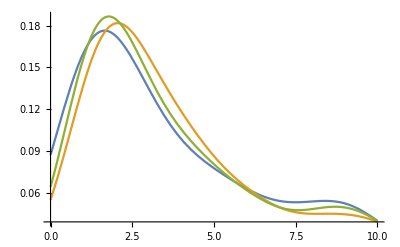

```mathematica
Plot[{PDF[trunkEngP[1],x],PDF[trunkEngN[1],x],PDF[trunkEng[1],x]},{x,0,10}]
```

## LLP flux calculation

The overall form of this expression is: kaon energy distribution X kaons produced per proton X proton flux in a given energy bin

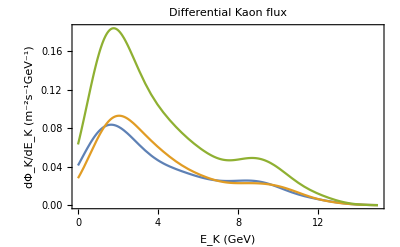

```mathematica
Plot[{4Pi*Evaluate[PDF[trunkEngP[1],x]]*numPKaons[1]/(2*10^4)*( intEB[
kaonPData[1][[1,3]]]* energyWidth[[1]]),4Pi*Evaluate[PDF[trunkEngN[1],x]]*numNKaons[1]/(2*10^4)*( intEB[
kaonNData[1][[1,3]]]* energyWidth[[1]]),4Pi*Evaluate[PDF[trunkEng[1],x]]*numKaons[1]/(2*10^4)*( intEB[
kaonPData[1][[1,3]]]* energyWidth[[1]])},{x,0,15},Frame->True,FrameLabel->{"E_K (GeV)","dΦ_K/dE_K (m^-2s^-1GeV^-1)"},PlotLabel->"Differential Kaon flux"]
```

1st line is just one low energy (18 GeV) trial bin, the 2nd is all protons under 30 GeV, the 3rd is all under 50 GeV, the 4th is under 100 GeV, and the final is all energies that the data I’m using has information for.

```mathematica
dKFlux18GeV=4Pi*Evaluate[PDF[trunkEng[1],x]]*numKaons[1]/(2*10^4)*( intEB[
kaonPData[1][[1,3]]]* energyWidth[[1]]);
dKFluxSub30=4Pi*Sum[Evaluate[PDF[trunkEng[i],x]]*numKaons[i]/(2*10^4)*( intEB[
kaonPData[i][[1,3]]]* energyWidth[[i]]),{i,1,5}];
dKFluxSub50 = 4Pi*Sum[Evaluate[PDF[trunkEng[i],x]]*numKaons[i]/(2*10^4)*( intEB[
kaonPData[i][[1,3]]]* energyWidth[[i]]),{i,1,10}];
dKFluxSub100 =4Pi*Sum[Evaluate[PDF[trunkEng[i],x]]*numKaons[i]/(2*10^4)*( intEB[
kaonPData[i][[1,3]]]* energyWidth[[i]]),{i,1,16}];
dKFluxAll =4Pi*Sum[Evaluate[PDF[trunkEng[i],x]]*numKaons[i]/(2*10^4)*( intEB[
kaonPData[i][[1,3]]]* energyWidth[[i]]),{i,1,20}];
```

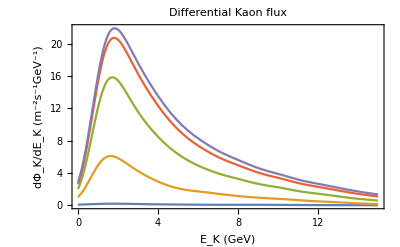

```mathematica
Plot[{dKFlux18GeV,dKFluxSub30,dKFluxSub50,dKFluxSub100,dKFluxAll},{x,0,15},Frame->True,FrameLabel->{"E_K (GeV)","dΦ_K/dE_K (m^-2s^-1GeV^-1)"},PlotLabel->"Differential Kaon flux"]
```

## Geometry

Here, I introduce all the equations required for the geometry calculations including detector parameters.

```mathematica
L[θ_,R_,h_]:=R*Cos[θ]+Sqrt[h^2 + 2R*h+R^2 *Cos[θ]^2](*In km*)
G[R_,h_]:=N[Integrate[Evaluate[Sin[θ]*((R+h)/L[θ,R,h])(1+((R*Cos[θ])/(L[θ,R,h]-R*Cos[θ])))],{θ,0,Pi}]]
```

```mathematica
volSK=Pi*(14.9)^2*32.2; (*In m^3*)
volHK=8*volSK;
```

```mathematica
detectionTime = 365.25*10*24*3600; (*In s, assuming 10 year detection period*)
```

```mathematica
Gmod[R_,h_,phiEng_]:=NIntegrate[Evaluate[Sin[θ]*((R+h)/L[θ,R,h])(1+((R*Cos[θ])/(L[θ,R,h]-R*Cos[θ])))*Exp[-(L[θ,R,h]*1000)/disTravel[phiEng]]],{θ,0,Pi}](*This includes the exponential part of the number of events integral*)
```

## Scalar Kinematics

### Unchanging Inputs

```mathematica
pPhiCM[mPhi_] :=Sqrt[(mKaon^2 -(mPi + mPhi)^2)(mKaon^2 -(mPi - mPhi)^2)]/(2*mKaon);
ePhiCM[mPhi_] := Sqrt[pPhiCM[mPhi]^2 + mPhi^2];
ePhi[mPhi_,eK_,ctheta_] :=(eK/mKaon)(ePhiCM[mPhi]+pPhiCM[mPhi]Sqrt[1 - (mKaon^2)/(eK^2)]ctheta) ;
```

```mathematica
mKaon = 0.4937 ;(*In GeV*)
mPi = 0.1396 ;(*In GeV*)
ms=0.101;
mt=173;
md = 0.005;
CKMfactor = 3.07*10^(-4);
tauK = 1.24*10^(-8)*(1.5192675*10^(24));
```

```mathematica
minEng = 1;(*GeV*)
step=0.15; (*GeV*)
```

```mathematica
totFlux = 0;
For[s = 1, s< (15/step), s++,
x =minEng + (s-1)(step);
totFlux +=dKFluxAll*step;
]
totFlux
```

114.337

Define kinematic functions:

```mathematica
gamma[phiEng_] :=phiEng/mPhi (*phiEng in GeV*)
velPhi[phiEng_] := Sqrt[1-(1/gamma[phiEng]^2 )]*c(*outputs m/s^2*)
disTravel[phiEng_]:=gamma[phiEng]*velPhi[phiEng]*tauPhi;(*output in m*)
```

Define tau lifetime plot:

```mathematica
pointList = Import["llpLifetimePoints.csv"];
pointTable = Table[{pointList[[i,1]],pointList[[i,2]]},{i,1,Length[pointList]}];
intLT = Interpolation[pointTable,InterpolationOrder->1]
```

InterpolatingFunction[…]

Set up output file

```mathematica
PrependTo[CurrentValue[$FrontEndSession,"NotebookPath"],NotebookDirectory[]];
```

```mathematica
titleLine = "Run  mPhi       theta   events" ;
titleLine >>"PhiEventsV2.txt"
```

## Need to loop

```mathematica
angleVar = 0;
massVar = 0;
```

```mathematica
{{For[run = 1, run < 7701, run++,

(*Set ϕ mass and other inputs*)
mPhi = 10^( - (massVar)(0.06)); (*In GeV*)
If[mPhi ≤ 0.2,tauPhiPlot = 10^(-1.116*Log[10,mPhi]+0.4777), tauPhiPlot = intLT[mPhi]];(*In s, from scalar spectator plot*)
mixingAngle = 10^(-1 - (angleVar)(0.02));
tauPhi = tauPhiPlot(10^(-6)/mixingAngle)^2;
minPhiEng = mPhi+0.05; (*Adjust these for final integral over Ephi: must be larger than mPhi*)
engStep = 0.1;

(*Calculate ϕ branching ratio:*)
Fkpi = ((mKaon^2 -mPi^2)/(ms -md))*fkpi;
fkpi =0.96(1+0.02(mPhi^2)/mPi^2);
phiBR = 9*Sqrt[2]*tauK*mixingAngle^2 *Gf^3*mt^4*ms^2*CKMfactor^2*Fkpi^2pPhiCM[mPhi]/(512*Pi^5*mKaon^2);(*BR to scalar, from Arxiv:1312.2547. Note that I pulled in a 1/2mk into the pPhiCM*)
phiBR2 =Sin[mixingAngle]^2 *0.002*2pPhiCM[mPhi]/mKaon ;(*from Arxiv:1310.8042*)

(*Create total probability distribution*)
For[s = 1, s< (15/step), s++,
eK =minEng + (s-1)(step);
ePhiDist= UniformDistribution[{(eK/mKaon)(ePhiCM[mPhi]-pPhiCM[mPhi]Sqrt[1 - (mKaon^2)/(eK^2)]),
(eK/mKaon)(ePhiCM[mPhi]+pPhiCM[mPhi]Sqrt[1 - (mKaon^2)/(eK^2)])}];
truncEPhi[s] =TruncatedDistribution[{0,1000},ePhiDist];
];
For[s = 1, s< (15/step), s++,
eK =minEng + (s-1)(step);
x =minEng + (s-1)(step);
If[s == 1,totDist = truncEPhi[s],
t = 1;
fluxBelow = 0;
While[t< s,
x=minEng + (t-1)(step);
fluxBelow += dKFluxAll;
t++;
];
x=minEng + (s-1)(step);
fluxAt =dKFluxAll;
totDist=MixtureDistribution[{fluxBelow,fluxAt},{totDist,truncEPhi[s]}]  ]
];
NumberOfEvents=Floor[volHK*detectionTime*
Sum[engStep*Gmod[6400,10,minPhiEng + i*engStep]*phiBR*PDF[totDist,minPhiEng+i*engStep]*totFlux/disTravel[minPhiEng+i*engStep],
{i,1,149}]];
dataLine =" "<> ToString[run]<>"   "<>ToString[mPhi]<>"   " <>ToString[N[mixingAngle]]<>"  "<>ToString[NumberOfEvents];
PutAppend[dataLine,"PhiEventsV2.txt"];

(*Increment variables*)
massVar++;
If[Mod[run,51]== 0,massVar =0;angleVar++;];
If[Mod[run,10] == 0,Print[run]];
];}, {}}
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

10

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.94524616435813}. NIntegrate obtained 8.3×10^-322 and 0. for the integral and error estimates.

General::munfl: 0.1 2.44558×10^-308 is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.12280279734375}. NIntegrate obtained 1.93362×10^-319 and 1.×10^-323 for the integral and error estimates.

General::munfl: 0.1 3.86389×10^-308 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 5.9443×10^-306 0.0000962042 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

20

30

40

50

60

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.1318194163030965808391936633370278286747634410858154296875}. NIntegrate obtained 6.5×10^-322 and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

70

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

80

90

100

110

120

130

140

150

160

170

180

190

200

210

220

230

240

250

260

270

280

290

300

310

320

330

340

350

360

370

380

390

400

410

420

430

440

450

460

470

480

490

500

510

520

530

540

550

560

570

580

590

600

610

620

630

640

650

660

670

680

690

700

710

720

730

740

750

760

770

780

790

800

810

820

830

840

850

860

870

880

890

900

910

920

930

940

950

960

970

980

990

1000

1010

1020

1030

1040

1050

1060

1070

1080

1090

1100

1110

1120

1130

1140

1150

1160

1170

1180

1190

1200

1210

1220

1230

1240

1250

1260

1270

1280

1290

1300

1310

1320

1330

1340

1350

1360

1370

1380

1390

1400

1410

1420

1430

1440

1450

1460

1470

1480

1490

1500

1510

1520

1530

1540

1550

1560

1570

1580

1590

1600

1610

1620

1630

1640

1650

1660

1670

1680

1690

1700

1710

1720

1730

1740

1750

1760

1770

1780

1790

1800

1810

1820

1830

1840

1850

1860

1870

1880

1890

1900

1910

1920

1930

1940

1950

1960

1970

1980

1990

2000

2010

2020

2030

2040

2050

2060

2070

2080

2090

2100

2110

2120

2130

2140

2150

2160

2170

2180

2190

2200

2210

2220

2230

2240

2250

2260

2270

2280

2290

2300

2310

2320

2330

2340

2350

2360

2370

2380

2390

2400

2410

2420

2430

2440

2450

2460

2470

2480

2490

2500

2510

2520

2530

2540

2550

2560

2570

2580

2590

2600

2610

2620

2630

2640

2650

2660

2670

2680

2690

2700

2710

2720

2730

2740

2750

2760

2770

2780

2790

2800

2810

2820

2830

2840

2850

2860

2870

2880

2890

2900

2910

2920

2930

2940

2950

2960

2970

2980

2990

3000

3010

3020

3030

3040

3050

3060

3070

3080

3090

3100

3110

3120

3130

3140

3150

3160

3170

3180

3190

3200

3210

3220

3230

3240

3250

3260

3270

3280

3290

3300

3310

3320

3330

3340

3350

3360

3370

3380

3390

3400

3410

3420

3430

3440

3450

3460

3470

3480

3490

3500

3510

3520

3530

3540

3550

3560

3570

3580

3590

3600

3610

3620

3630

3640

3650

3660

3670

3680

3690

3700

3710

3720

3730

3740

3750

3760

3770

3780

3790

3800

3810

3820

3830

3840

3850

3860

3870

3880

3890

3900

3910

3920

3930

3940

3950

3960

3970

3980

3990

4000

4010

4020

4030

4040

4050

4060

4070

4080

4090

4100

4110

4120

4130

4140

4150

4160

4170

4180

4190

4200

4210

4220

4230

4240

4250

4260

4270

4280

4290

4300

4310

4320

4330

4340

4350

4360

4370

4380

4390

4400

4410

4420

4430

4440

4450

4460

4470

4480

4490

4500

4510

4520

4530

4540

4550

4560

4570

4580

4590

4600

4610

4620

4630

4640

4650

4660

4670

4680

4690

4700

4710

4720

4730

4740

4750

4760

4770

4780

4790

4800

4810

4820

4830

4840

4850

4860

4870

4880

4890

4900

4910

4920

4930

4940

4950

4960

4970

4980

4990

5000

5010

5020

5030

5040

5050

5060

5070

5080

5090

5100

5110

5120

5130

5140

5150

5160

5170

5180

5190

5200

5210

5220

5230

5240

5250

5260

5270

5280

5290

5300

5310

5320

5330

5340

5350

5360

5370

5380

5390

5400

5410

5420

5430

5440

5450

5460

5470

5480

5490

5500

5510

5520

5530

5540

5550

5560

5570

5580

5590

5600

5610

5620

5630

5640

5650

5660

5670

5680

5690

5700

5710

5720

5730

5740

5750

5760

5770

5780

5790

5800

5810

5820

5830

5840

5850

5860

5870

5880

5890

5900

5910

5920

5930

5940

5950

5960

5970

5980

5990

6000

6010

6020

6030

6040

6050

6060

6070

6080

6090

6100

6110

6120

6130

6140

6150

6160

6170

6180

6190

6200

6210

6220

6230

6240

6250

6260

6270

6280

6290

6300

6310

6320

6330

6340

6350

6360

6370

6380

6390

6400

6410

6420

6430

6440

6450

6460

6470

6480

6490

6500

6510

6520

6530

6540

6550

6560

6570

6580

6590

6600

6610

6620

6630

6640

6650

6660

6670

6680

6690

6700

6710

6720

6730

6740

6750

6760

6770

6780

6790

6800

6810

6820

6830

6840

6850

6860

6870

6880

6890

6900

6910

6920

6930

6940

6950

6960

6970

6980

6990

7000

7010

7020

7030

7040

7050

7060

7070

7080

7090

7100

7110

7120

7130

7140

7150

7160

7170

7180

7190

7200

7210

7220

7230

7240

7250

7260

7270

7280

7290

7300

7310

7320

7330

7340

7350

7360

7370

7380

7390

7400

7410

7420

7430

7440

7450

7460

7470

7480

7490

7500

7510

7520

7530

7540

7550

7560

7570

7580

7590

7600

7610

7620

7630

7640

7650

7660

7670

7680

7690

7700

{{Null},{Null}}

```mathematica
massVar =0;
angleVar =0;
```

```mathematica
For[run=1, run<50, run++,

massVar++;
If[Mod[run,21]== 1,massVar =0;angleVar++;];
Print[run," ", massVar," ",angleVar]

]
```

1 0 1

2 1 1

3 2 1

4 3 1

5 4 1

6 5 1

7 6 1

8 7 1

9 8 1

10 9 1

11 10 1

12 11 1

13 12 1

14 13 1

15 14 1

16 15 1

17 16 1

18 17 1

19 18 1

20 19 1

21 20 1

22 0 2

23 1 2

24 2 2

25 3 2

26 4 2

27 5 2

28 6 2

29 7 2

30 8 2

31 9 2

32 10 2

33 11 2

34 12 2

35 13 2

36 14 2

37 15 2

38 16 2

39 17 2

40 18 2

41 19 2

42 20 2

43 0 3

44 1 3

45 2 3

46 3 3

47 4 3

48 5 3

49 6 3